```mathematica
SetDirectory@NotebookDirectory[]
Import["esmlib_nsl.wl"]
```

/home/eric/git/nonlinear-systems-lab

## Equation Manipulation

```mathematica
eqs={θ1''[t]+2γ θ1'[t]+θ1[t]==-y''[t],
θ2''[t]+2γ θ2'[t]+θ2[t]==-y''[t],
y''[t]+2 Γ y'[t]==-μ(θ1''[t]+θ2''[t])};
Column@eqs//TraditionalForm
```

2 γ θ1'(t)+θ1''(t)+θ1(t)==-y''(t)
2 γ θ2'(t)+θ2''(t)+θ2(t)==-y''(t)
y''(t)+2 Γ y'(t)==-μ (θ1''(t)+θ2''(t))

Make first-order

```mathematica
eqs/.<|θ1''[t]:>ω1'[t],θ1'[t]:>ω1[t],
θ2''[t]:>ω2'[t],θ2'[t]:>ω2[t]|>//Column//TraditionalForm
```

2 γ ω1(t)+θ1(t)+ω1'(t)==-y''(t)
2 γ ω2(t)+θ2(t)+ω2'(t)==-y''(t)
y''(t)+2 Γ y'(t)==-μ (ω1'(t)+ω2'(t))

## Matrix Stuff

```mathematica
A=({{1, □, □, □, □, □}, {□, 1, □, □, □, 1}, {□, □, 1, □, □, □}, {□, □, □, 1, □, 1}, {□, □, □, □, 1, □}, {□, μ, □, μ, □, 1}})/.□->0;
A//MatrixForm
B=({{□, 1, □, □, □, □}, {-1, -2γ, □, □, □, □}, {□, □, □, 1, □, □}, {□, □, -1, -2γ, □, □}, {□, □, □, □, □, 1}, {□, □, □, □, □, -2Γ}})/.□->0;
B//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | μ | 0 | μ | 0 | 1)

(0 | 1 | 0 | 0 | 0 | 0
-1 | -2 γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | -2 γ | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | -2 Γ)

```mathematica
Inverse[A].B//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
-(1-μ)/(1-2 μ) | -(2 γ (1-μ))/(1-2 μ) | -μ/(1-2 μ) | -(2 γ μ)/(1-2 μ) | 0 | (2 Γ)/(1-2 μ)
0 | 0 | 0 | 1 | 0 | 0
-μ/(1-2 μ) | -(2 γ μ)/(1-2 μ) | -(1-μ)/(1-2 μ) | -(2 γ (1-μ))/(1-2 μ) | 0 | (2 Γ)/(1-2 μ)
0 | 0 | 0 | 0 | 0 | 1
μ/(1-2 μ) | (2 γ μ)/(1-2 μ) | μ/(1-2 μ) | (2 γ μ)/(1-2 μ) | 0 | -(2 Γ)/(1-2 μ))

## Nonlinear Pendulum

```mathematica
escapement=If[Abs[θ[t]]≤escang/2 && ω[t]>0,fesc,0]
eqs={
θ'[t]==ω[t],
ω'[t]==-Sin[θ[t]]-2γ ω[t] Abs[ω[t]]-γ2 Sign[ω[t]]+esc[t],
esc[t]==If[Abs[θ[t]]<escang/2 && ω[t]>0,escE/escang,0]};
Column[eqs,Frame->All]//TraditionalForm
```

If[Abs[θ[t]]≤escang/2&&ω[t]>0,fesc,0]

(TraditionalForm )[θ'[t]==ω[t]
ω'[t]==esc[t]-γ2 Sign[ω[t]]-Sin[θ[t]]-2 γ Abs[ω[t]] ω[t]
esc[t]==If[Abs[θ[t]]<escang/2&&ω[t]>0,escE/escang,0]]

{θ[0]==0.2,ω[0]==0}

<|γ→0.05,γ2→0.0001,escang→0.0261799,escE→0.005|>

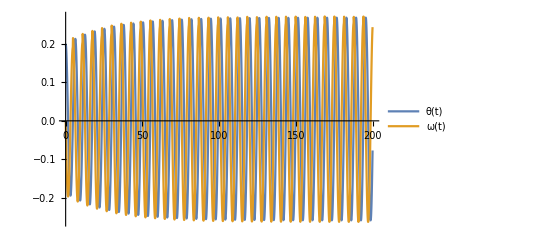

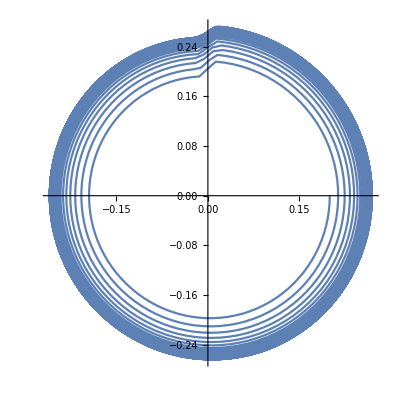

```mathematica
initialConds={θ[0]==.2,ω[0]==0}
params=<|γ->0.05,γ2->0.0001,escang->1.5*Degree,escE->0.005|>
sol=NDSolve[{eqs,initialConds}/.params,{θ[t],ω[t]},{t,0,200}][[1]];
IFPlot[sol]
ParametricPlot[{θ[t],ω[t]}/.sol,{t,0,sol[[1,2,0]]["Domain"][[1,2]]}]
```